```mathematica
Lx := 1
Ly := 1
H := 1
xs := 0
ys := 0
```

```mathematica
XR[x_, n_] := Sqrt[2 / Lx] Cos[Pi n / Lx (x + Lx / 2)] 
YR[y_, m_] := Sqrt[2 / Ly] Cos[Pi m / Ly y]
```

```mathematica
enR[n_, m_] := (Pi n / Lx)^2 + (Pi m / Ly)^2
```

```mathematica
Yw[y_, m_] := Sqrt[2 / H] Cos[Pi m / H y]
```

```mathematica
GR[x_, y_, xs_, ys_, EE_, maxn_] := Sum[XR[x, n] YR[y, m] XR[xs, n] YR[ys, m] / (en[n, m] - EE),{n,0,maxn},{m,0,maxn}]
```

```mathematica
Gx[x_, xs_, EE_] := -I / (2 Sqrt[EE]) Exp[I Sqrt[EE] Abs[x - xs]]
GW[x_, y_, xs_, ys_, EE_, maxn_] := Sum[ Yw[y, m] Yw[ys, m] Gx[x, xs, EE - (Pi m / H)^2 ],{m, 0, maxn}]
```

```mathematica
E0[delta_] := (I / delta Exp[-EulerGamma])^2
```

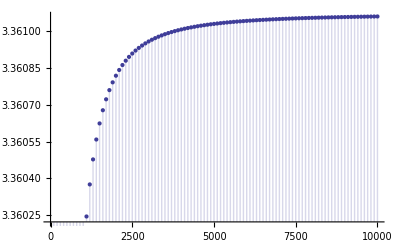

```mathematica
DiscretePlot[Norm[GW[xs, ys, xs, ys, 10.0, maxn] - GW[xs, ys, xs, ys, E0[0.001], maxn]], {maxn, 0, 10000, 100}]
```

```mathematica
GW[xs, ys, xs, ys, E0[0.001], 1000]
```

-0.772307+0. ⅈ

```mathematica
Norm[GW[xs, ys, xs, ys, 10.0, 5000]  - GW[xs, ys, xs, ys, E0[0.001], 5000]]
```

3.36103

```mathematica
Norm[GW[xs, ys, xs, ys, 10.0, 100] - GW[xs, ys, xs, ys, E0[0.001], 100]]
```

3.31047

```mathematica
Norm[GR[xs, ys, xs, ys, 10.0, 1000]]
```

28.6348

```mathematica
Norm[GR[xs, ys, xs, ys, 10.0, 1000] - GR[xs, ys, xs, ys, E0[0.001], 1000]]
```

29.2247

```mathematica
DiscretePlot[Norm[GR[xs, ys, xs, ys, 1.0, maxn] - GR[xs, ys, xs, ys, E0[0.001], maxn]],{maxn,0, 100}]
```

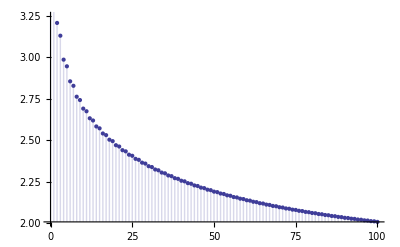

```mathematica
EE := 1
```